# Optimization of the Irreversible Stirling cycle in the limit θ_max->∞, θ_min->0

```mathematica
ClearAll["Global`*"]
```

```mathematica
SetDirectory["C:\\Users\\DirName"]
```

```mathematica
dir = Directory[];
```

```mathematica
<<MaTeX`
```

## Cycle parameters

```mathematica
Wqs[ν_,χ_]:=(1-ν)/2 Log[χ];
A[χ_]:=(1/(√χ)-1)^2;
w[ν_,χ_]:=(-Wqs[ν,χ])/(A[χ]*(1+√ν)^2);
tisoc[ν_,χ_]:=-1/(2χ)Log[ν];
σ[ν_,χ_]:=√(1+w[ν,χ]*tisoc[ν,χ]);
sAB[ν_,χ_]:=(1+σ[ν,χ])/(w[ν,χ]*(1+√ν));
sCD[ν_,χ_]:=√ν*sAB[ν,χ];
WAB[ν_,χ_]:=Log[χ]/2+A[χ]/sAB[ν,χ];
WCD[ν_,χ_]:=(-ν*Log[χ])/2+(ν*A[χ])/sCD[ν,χ];
P[ν_,χ_]:=-(WAB[ν,χ]+WCD[ν,χ])/(sAB[ν,χ]+sCD[ν,χ]+tisoc[ν,χ]);
η[ν_,χ_]:=1+WCD[ν,χ]/WAB[ν,χ];
ηC[ν_]:=1-ν;
ηCA[ν_]:=1-√ν;
ηplus[ν_]:=ηC[ν]/(2-ηC[ν])
```

## Auxiliary Ticks functions

```mathematica
STicks[xm_,xM_,ΔxM_,Δxm_]:=Join[Table[{x,"",{0.02,0},Thickness[0.004]},{x,xm,xM,ΔxM}],Table[{x,"",{0.01,0},Thickness[0.002]},{x,xm,xM,Δxm}]];
LTicks[xm_,xM_,ΔxM_,Δxm_,n_,m_]:=Join[Table[{x,NumberForm[x,{n,m}],{0.02,0},Thickness[0.004]},{x,xm,xM,ΔxM}],Table[{x,"",{0.01,0},Thickness[0.002]},{x,xm,xM,Δxm}]];
LTicksLegend[xm_,xM_,ΔxM_,Δxm_,n_,m_]:=Join[Table[{x,NumberForm[x,{m,n}],{0.02,0},Thickness[0.004]},{x,xm,xM,ΔxM}],Table[{x,"",{0.01,0},Thickness[0.002]},{x,xm,xM,Δxm}]];

LTicksThin[xm_,xM_,ΔxM_,Δxm_,n_,m_]:=Join[Table[{x,NumberForm[x,{n,m}],{0.02,0},Thickness[0.003]},{x,xm,xM,ΔxM}],Table[{x,"",{0.01,0},Thickness[0.002]},{x,xm,xM,Δxm}]];
STicksThin[xm_,xM_,ΔxM_,Δxm_]:=Join[Table[{x,"",{0.02,0},Thickness[0.003]},{x,xm,xM,ΔxM}],Table[{x,"",{0.01,0},Thickness[0.002]},{x,xm,xM,Δxm}]];

LTicksInset[xm_,xM_,ΔxM_,Δxm_]:=Join[Table[{x,Round[1000*x],{0.02,0},Thickness[0.005]},{x,xm,xM,ΔxM}],Table[{x,"",{0.01,0},Thickness[0.002]},{x,xm,xM,Δxm}]];
```

## Figure 3. Density plots: P̃(ν,χ), η̃(ν,χ)

```mathematica
L=200; 
am=10^-6;
bm = 0.1;
aM = 10^-6;
bM = 1-10^-6;
δm = (bm-am)/(L-1);
δM = (bM-aM)/(L-1);

AuxTableFig2s1=Flatten[Table[{ν,χ,P[ν,χ]},{ν,am,bm,δm },{χ,aM,bM,δM}],1];
```

```mathematica
L=300; 
am= 0.1;
bm = 1-10^-6;
aM = 10^-6;
bM = 1-10^-6;
δm = (bm-am)/(L-1);
δM = (bM-aM)/(L-1);

AuxTableFig2s2=Flatten[Table[{ν,χ,P[ν,χ]},{ν,am,bm,δm },{χ,aM,bM,δM}],1];
```

```mathematica
AuxTableFig2 = Join[AuxTableFig2s1,AuxTableFig2s2];
```

```mathematica
Export[dir<>"\\Data\\AuxTableFig2.dat",AuxTableFig2,"Table"];
```

```mathematica
AuxTableFig2=Import[dir<>"\\Data\\AuxTableFig2.dat"];
```

```mathematica
LauxFig2 = Length[AuxTableFig2];
```

```mathematica
xm=0;xM=1;Δxm=0.1;ΔxM=0.2;
ym=0;yM=1;Δym=0.1;ΔyM=0.2;
max=0.042;min=0;step=0.01;Colors="Rainbow";
magnif = 2;


DP01=Show[ListDensityPlot[Table[AuxTableFig2[[i]],{i,1,LauxFig2}],InterpolationOrder->3,PlotRange->All,PlotRangePadding->None,ColorFunction->Colors,PlotLegends->BarLegend[{Colors,{min,max}},Ticks->LTicksLegend[min,max,step,step/2,2,1],LegendMarkerSize->250,LegendLabel->MaTeX["\\widetilde{\\mathcal{P}}(\\nu,\\chi)",Magnification->magnif],LegendMargins->{{-4,0},{35,0}}],LabelStyle->Directive[Black,16,FontFamily->"Times New Roman"],RotateLabel->False,Axes->False,FrameStyle->Directive[Black,20,FontFamily->"Times New Roman",Thickness[0.004]],FrameLabel->{MaTeX["\\nu",Magnification->magnif],MaTeX["\\chi",Magnification->magnif]},ImageSize->Medium,FrameTicks->{{LTicks[ym,yM,ΔyM,Δym,2,1],STicks[ym,yM,ΔyM,Δym]},{LTicks[xm,xM,ΔxM,Δxm,1,1],STicks[xm,xM,ΔxM,Δxm]}},PlotRangeClipping->False],Graphics[ListContourPlot[Table[AuxTableFig2[[i]],{i,1,LauxFig2}],PlotRange->All,Contours->Table[x,{x,min,max,step/2}],ContourShading->False,ContourStyle->White]],PlotRange->{{xm,xM},{ym,yM}}]
```

-Graphics-

```mathematica
L=200; 
am=10^-6;
bm = 1-10^-6;
aM = 10^-6;
bM = 0.1;
δm = (bm-am)/(L-1);
δM = (bM-aM)/(L-1);

AuxDP02s1=Flatten[Table[{ν,χ,η[ν,χ]},{ν,am,bm,δm },{χ,aM,bM,δM}],1];
```

```mathematica
L=300; 
am=10^-6;
bm = 1-10^-6;
aM = 0.1;
bM = 0.9;
δm = (bm-am)/(L-1);
δM = (bM-aM)/(L-1);

AuxDP02s2=Flatten[Table[{ν,χ,η[ν,χ]},{ν,am,bm,δm },{χ,aM,bM,δM}],1];
```

```mathematica
L=200; 
am=10^-6;
bm = 1-10^-6;
aM = 0.9;
bM = 1-10^-6;
δm = (bm-am)/(L-1);
δM = (bM-aM)/(L-1);

AuxDP02s3=Flatten[Table[{ν,χ,η[ν,χ]},{ν,am,bm,δm },{χ,aM,bM,δM}],1];
```

```mathematica
AuxDP02 = Join[AuxDP02s1,AuxDP02s2,AuxDP02s3];
```

```mathematica
Export[dir<>"\\Data\\AuxDP02.dat",AuxDP02,"Table"];
```

```mathematica
AuxDP02=Import[dir<>"\\Data\\AuxDP02.dat"];
```

```mathematica
LAuxDP02 = Length[AuxDP02];
```

```mathematica
xm=0;xM=1;Δxm=0.1;ΔxM=0.2;
ym=0;yM=1;Δym=0.1;ΔyM=0.2;
max=1;min=0;step=0.2;Colors="Rainbow";
magnif = 2;

DP02=Show[ListDensityPlot[Table[AuxDP02[[i]],{i,1,LAuxDP02}],InterpolationOrder->3,PlotRange->All,PlotRangePadding->None,ColorFunction->Colors,PlotLegends->BarLegend[{Colors,{min,max}},Ticks->LTicksLegend[min,max,step,step,1,1],LegendMarkerSize->250,LegendLabel->MaTeX["\\tilde{\\eta}(\\nu,\\chi)",Magnification->magnif],LegendMargins->{{-4,0},{35,0}}],LabelStyle->Directive[Black,16,FontFamily->"Times New Roman"],RotateLabel->False,Axes->False,FrameStyle->Directive[Black,20,FontFamily->"Times New Roman",Thickness[0.004]],FrameLabel->{MaTeX["\\nu",Magnification->magnif],MaTeX["\\chi",Magnification->magnif]},ImageSize->Medium,FrameTicks->{{LTicks[ym,yM,ΔyM,Δym,2,1],STicks[ym,yM,ΔyM,Δym]},{LTicks[xm,xM,ΔxM,Δxm,1,1],STicks[xm,xM,ΔxM,Δxm]}},PlotRangeClipping->False],Graphics[ListContourPlot[Table[AuxDP02[[i]],{i,1,LAuxDP02}],PlotRange->All,Contours->Table[x,{x,min,max,step}],ContourShading->False,ContourStyle->White]],PlotRange->{{xm,xM},{ym,yM}}]
```

-Graphics-

## Optimization over the compression ratio: χ^*(ν), (P̃)^*(ν),(η̃)^*(ν)

```mathematica
pχopt[ν_]:=FindMaximum[{P[ν,χ],0<χ<1},{χ,1-1/2(1-ν)-1/48(1-ν)^2+11/1152(1-ν)^3}]
popt[ν_]:=First[pχopt[ν]]
χopt[ν_]:=χ/.Last[pχopt[ν]]
ηopt[ν_]:=η[ν,χopt[ν]];
```

```mathematica
fχoptAux[ν_]:=FindMaximum[{Exp[P[ν,χ]+5],0.9<χ<1},{χ,1-1/2(1-ν)-1/48(1-ν)^2+11/1152(1-ν)^3}]
χoptAux[ν_]:=χ/.Last[fχoptAux[ν]]
```

### Numerical study

```mathematica
δ=10^-6;
xs:=Table[x,{x,0.99,1-δ,δ}];
vs[ν_]:=Table[P[ν,x],{x,0.99,1-δ,δ}]
χoptAux2[ν_]:=xs[[Ordering[vs[ν],-1]]][[1]];
plim1=0.90;
plim2=0.99;
Δ=10^-3;
χsOptA:=Table[{N[ν],χopt[ν]},{ν,Δ,plim1-Δ,Δ}]
χsOptB:=Table[{ν,χoptAux[ν]},{ν,plim1,plim2-Δ,Δ}]
χsOptC:=Table[{ν,χoptAux2[ν]},{ν,plim2,1-Δ,Δ}]
χsOpt:=Join[χsOptA,χsOptB,χsOptC]
```

```mathematica
δ1=10^-3;
δ2=0.5*10^-4;
tableχP1[c_]:=Flatten[MaximalBy[Table[{χ,P[1-c,χ]},{χ,0.5,1-δ1,δ1}],Last]];
tableχP2[c_]:=Flatten[MaximalBy[Table[{χ,P[1-c,χ]},{χ,0.1,1-δ2,δ2}],Last]]
```

```mathematica
χoptNumTable1=Table[{c,tableχP1[c][[1]]},{c,0.0001,0.95,0.033}];
```

```mathematica
χoptNumTable2=Table[{c,tableχP2[c][[1]]},{c,0.95,1,0.033}];
```

```mathematica
χoptNumTableCheck = Join[χoptNumTable1,χoptNumTable2];
```

```mathematica
δ1=10^-5;
δ2=10^-4;
tableχP3[c_]:=Flatten[MaximalBy[Table[{χ,P[1-c,χ]},{χ,0.5,1-δ1,δ1}],Last]]
```

```mathematica
χoptNumTableCheck2=Table[{c,tableχP3[c][[1]]-(1-c/2)},{c,0.0001,0.4,0.0125}];
```

```mathematica
Export[dir<>"\\Data\\ChisOpt.dat",χsOpt,"Table"];
Export[dir<>"\\Data\\ChiOptNumTableCheck.dat",χoptNumTableCheck,"Table"];Export[dir<>"\\Data\\ChiOptNumTableCheck2.dat",χoptNumTableCheck2,"Table"];
```

```mathematica
χoptNumTableCheck=Import[dir<>"\\Data\\ChiOptNumTableCheck.dat"];
χoptNumTableCheck2=Import[dir<>"\\Data\\ChiOptNumTableCheck2.dat"];
χsOpt=Import[dir<>"\\Data\\ChisOpt.dat"];
```

```mathematica
fχsOpt=Interpolation[χsOpt];
```

```mathematica
νopt:=ν/.Last[FindMaximum[{P[ν,fχsOpt[ν]],0<ν<1},{ν,0.08}]]
```

```mathematica
{νopt,fχsOpt[νopt],P[νopt,fχsOpt[νopt]]}
```

{0.0604619,0.507215,0.0413035}

## Figure 4

```mathematica
colorCurve= RGBColor[0.5,0,0.5];
colorPoint = RGBColor[0.4,0,0.4];
```

```mathematica
colorCurve2 = RGBColor[0.7,0,0];
colorPoint2 = RGBColor[0.5,0,0];
```

```mathematica
marker1=Graphics[{colorPoint,Rectangle[]}];
marker2=Graphics[{colorPoint2,Rectangle[]}];
```

```mathematica
νp = 0.5;
xm=0;xM=1;Δxm=0.1;ΔxM=0.2;
ym=0;yM=1;Δym=0.1;ΔyM=0.2;
max=0.042;min=0;step=0.01;Colors="Rainbow";
magnif = 2;
pointSize = 0.035;
th = 0.008;
Δ=10^-3;

DPfig4aux=Show[ListDensityPlot[Table[AuxTableFig2[[i]],{i,1,LauxFig2}],InterpolationOrder->3,PlotRange->All,PlotRangePadding->None,ColorFunction->Colors,PlotLegends->Placed[BarLegend[{Colors,{min,max}},Ticks->LTicksLegend[min,max,step,step/4,2,2],LegendMarkerSize->500,LegendLabel->MaTeX["\\widetilde{\\mathcal{P}}(\\nu,\\chi)",Magnification->magnif],LegendMargins->{{-4,0},{35,0}}],Left],LabelStyle->Directive[Black,20,FontFamily->"Times New Roman"],RotateLabel->False,Axes->False,FrameStyle->Directive[Black,20,FontFamily->"Times New Roman",Thickness[0.004]],FrameLabel->{MaTeX["\\nu",Magnification->magnif],MaTeX["\\chi",Magnification->magnif]},FrameTicks->{{LTicks[ym,yM,ΔyM,Δym,2,1],STicks[ym,yM,ΔyM,Δym]},{LTicks[xm,xM,ΔxM,Δxm,1,1],STicks[xm,xM,ΔxM,Δxm]}},PlotRangeClipping->False],Graphics[ListContourPlot[Table[AuxTableFig2[[i]],{i,1,LauxFig2}],PlotRange->All,Contours->Table[x,{x,min,max,step/2}],ContourShading->False,ContourStyle->White]],ParametricPlot[{ν,fχsOpt[ν]},{ν,Δ,1},PlotStyle->{Thickness[0.01],Dashed,Black}],Graphics[{PointSize[pointSize],Black,Point[{νopt,fχsOpt[νopt]}]}],ParametricPlot[{νp,χ},{χ,0,1},PlotStyle->{Thickness[th],colorCurve}],ListPlot[{{νp,fχsOpt[νp]}},PlotMarkers->{{marker1,pointSize}}],ParametricPlot[{νopt,χ},{χ,0,1},PlotStyle->{Thickness[th],colorCurve2}],ListPlot[{{νopt,fχsOpt[νopt]}},PlotMarkers->{{marker2,pointSize}}],PlotRange->{{xm,xM},{ym,yM}},PlotRangeClipping->True,ImageSize->Large];

DPfig4=Show[DPfig4aux,Graphics[{White,EdgeForm[None],Polygon[{{0,1},{1,1},{1,1.1},{0,1.1}}->{{-1,-0.5},{1,-0.5},{1,0.5},{-1,0.5}}]}]]
```

-Graphics-

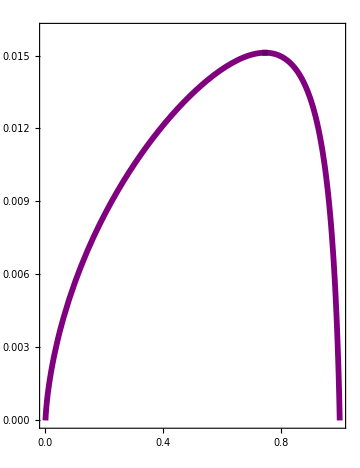

```mathematica
xm=0;xM=1;Δxm=0.1;ΔxM=0.2;
ym=0;yM=0.016;Δym=0.001;ΔyM=0.003;
magnif=2;
Fig4nu0d5=Show[Plot[P[νp,χ],{χ,0,1},PlotRange->All,PlotStyle->{colorCurve,Thickness[1.45*th]}],ListPlot[{{fχsOpt[νp],P[νp,fχsOpt[νp]]}},PlotMarkers->{{marker1,1.4*pointSize}},PlotRange->All],PlotRange->{{xm,xM},{ym,yM}},AspectRatio->1.3,FrameTicks->{{LTicks[ym,yM,ΔyM,Δym,2,3],STicks[ym,yM,ΔyM,Δym]},{LTicks[xm,xM,ΔxM,Δxm,2,1],STicks[xm,xM,ΔxM,Δxm]}},PlotRangeClipping->True,PlotRangePadding->None,
LabelStyle->Directive[Black,16,FontFamily->"Times New Roman"],RotateLabel->True,Axes->False,FrameStyle->Directive[Black,20,FontFamily->"Times New Roman",Thickness[0.004]],FrameLabel->{MaTeX["\\chi",Magnification->magnif],MaTeX["\\widetilde{\\mathcal{P}}(\\nu=0.5,\\chi)",Magnification->magnif]},Frame->True,ImageSize->Medium]
```

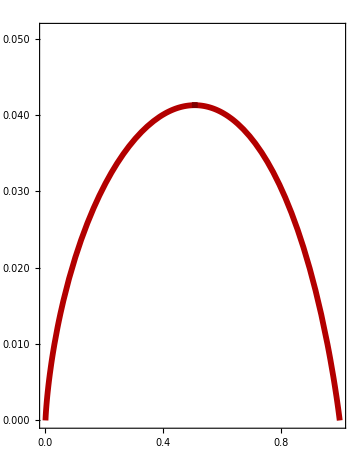

```mathematica
xm=0;xM=1;Δxm=0.1;ΔxM=0.2;
ym=0;yM=0.051;Δym=0.005;ΔyM=0.01;
magnif=2;
Fig4nuopt=Show[Plot[P[νopt,χ],{χ,0,1},PlotRange->All,PlotStyle->{colorCurve2,Thickness[1.45*th]}],ListPlot[{{fχsOpt[νopt],P[νopt,fχsOpt[νopt]]}},PlotMarkers->{{marker2,1.4*pointSize}},PlotRange->All],PlotRange->{{xm,xM},{ym,yM}},AspectRatio->1.3,FrameTicks->{{LTicks[ym,yM,ΔyM,Δym,2,3],STicks[ym,yM,ΔyM,Δym]},{LTicks[xm,xM,ΔxM,Δxm,2,1],STicks[xm,xM,ΔxM,Δxm]}},PlotRangeClipping->True,PlotRangePadding->None,
LabelStyle->Directive[Black,16,FontFamily->"Times New Roman"],RotateLabel->True,Axes->False,FrameStyle->Directive[Black,20,FontFamily->"Times New Roman",Thickness[0.004]],FrameLabel->{MaTeX["\\chi",Magnification->magnif],MaTeX["\\widetilde{\\mathcal{P}}(\\nu=\\nu^*,\\chi)",Magnification->magnif]},Frame->True,ImageSize->Medium]
```

## Figure 5

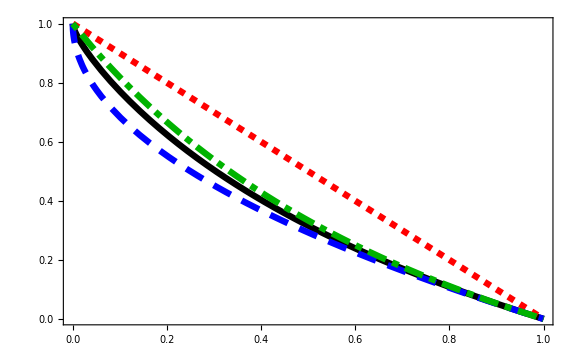

```mathematica
xm=0;xM=1;Δxm=0.1;ΔxM=0.2;
ym=0;yM=1;Δym=0.1;ΔyM=0.2;
magnif=2;
th = 0.008;color3 = RGBColor[0,0.7,0];Fig5=Show[Plot[{ηopt[ν],ηC[ν],ηCA[ν],ηC[ν]/(2-ηC[ν])},{ν,0,1},PlotStyle->{{Thickness[th],Black},{Thickness[th],Dashed,Red},{Thickness[th],Dashing[{Large,Medium,Large,Medium}],Blue},{Thickness[th],Dashing[{Small,Small,Large,Small}],color3}},PlotLegends->{MaTeX["\\tilde{\\eta}^*",Magnification->magnif],MaTeX["\\eta_C",Magnification->magnif],MaTeX["\\eta_{CA}",Magnification->magnif],MaTeX["\\eta_+",Magnification->magnif]}],PlotRange->{{xm,xM},{ym,yM}},AspectRatio->0.618,FrameTicks->{{LTicks[ym,yM,ΔyM,Δym,2,1],STicks[ym,yM,ΔyM,Δym]},{LTicks[xm,xM,ΔxM,Δxm,2,1],STicks[xm,xM,ΔxM,Δxm]}},PlotRangeClipping->True,PlotRangePadding->None,
LabelStyle->Directive[Black,16,FontFamily->"Times New Roman"],RotateLabel->True,Axes->False,FrameStyle->Directive[Black,20,FontFamily->"Times New Roman",Thickness[0.004]],FrameLabel->{MaTeX["\\nu",Magnification->magnif],MaTeX["\\eta",Magnification->magnif]},Frame->True,ImageSize->Large]
```

## Figure 6

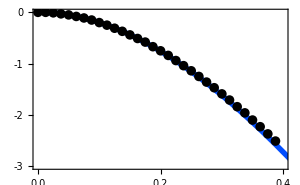
-Graphics--Graphics-

```mathematica
xm=0;xM=0.4;Δxm=0.05;ΔxM=0.1;
ym=-0.003;yM=0;Δym=0.0005;ΔyM=0.001;
magnif=1.3;
pointsize=0.023;
th = 0.013;
colorPointsNum = RGBColor[0,0,0];
color3=RGBColor[0,0.3,1];

inset0=Show[Plot[{-1/48*c^2+11/1152*c^3},{c,0,1},PlotStyle->{{color3,Thickness[th]}}],ListPlot[χoptNumTableCheck2,PlotStyle->{colorPointsNum,PointSize[pointsize]}],PlotRange->{{xm,xM},{ym,yM}},AspectRatio->0.618,FrameTicks->{{LTicksInset[ym,yM,ΔyM,Δym],STicks[ym,yM,ΔyM,Δym]},{LTicks[xm,xM,ΔxM,Δxm,2,1],STicks[xm,xM,ΔxM,Δxm]}},PlotRangeClipping->True,PlotRangePadding->None,
LabelStyle->Directive[Black,16,FontFamily->"Times New Roman"],RotateLabel->True,Axes->False,FrameStyle->Directive[Black,15,FontFamily->"Times New Roman",Thickness[0.005]],FrameLabel->{MaTeX["\\eta_C",Magnification->magnif],MaTeX["\\chi^*-\\left(1-\\frac{\\eta_C}{2}\\right)",Magnification->magnif]},Frame->True,ImageSize->300];

inset1=Overlay[{Show[inset0,ImagePadding->{{Automatic,Automatic},{Automatic,20}}],Style[MaTeX["\\times10^{-3}",Magnification->0.95*magnif]]},Alignment->{-0.565,1},ImageSize->350]
```

```mathematica
xm=0;xM=1;Δxm=0.05;ΔxM=0.2;
ym=0.4;yM=1;Δym=0.05;ΔyM=0.1;
magnif=1.575;
magnif0 = 1.89;
pointsize=0.017;
th = 0.008;
Fig6=Show[Plot[{1-1/2*c-1/48*c^2+11/1152*c^3},{c,0,1},PlotLegends->Placed[{MaTeX["\\text{Cubic expansion in Eq.~(72)}",Magnification->magnif]},{0.705,0.85}],PlotStyle->{{color3,Thickness[th]}}],ListPlot[χoptNumTableCheck,PlotStyle->{colorPointsNum ,PointSize[pointsize]},PlotLegends->Placed[{MaTeX["\\hspace{8pt}\\text{Numerical}",Magnification->magnif]},{0.6,0.75}]],Graphics[Inset[inset1,{0.30,0.570},{0,0},{1,0.5}]],PlotRange->{{xm,xM},{ym,yM}},AspectRatio->0.675,FrameTicks->{{LTicksThin[ym,yM,ΔyM,Δym,2,1],STicksThin[ym,yM,ΔyM,Δym]},{LTicksThin[xm,xM,ΔxM,Δxm,2,1],STicksThin[xm,xM,ΔxM,Δxm]}},PlotRangeClipping->True,PlotRangePadding->None,
LabelStyle->Directive[Black,16,FontFamily->"Times New Roman"],RotateLabel->True,Axes->False,FrameStyle->Directive[Black,20,FontFamily->"Times New Roman",Thickness[0.003]],FrameLabel->{MaTeX["\\eta_C",Magnification->magnif0],MaTeX["\\chi^*",Magnification->magnif0]},Frame->True,ImageSize->690]
```

-Graphics-